```mathematica
<<mf23.m
```

```mathematica
Clear[c];
Clear[e];
ψ[z_]:=PolyGamma[z]; (* RHS is Mathematica-speak for the digamma function. *)
α[m_]:=(1/2)*(1/2-1/m);
β[m_]:=(1/2)*(1/2+1/m);
c[m_,ν_]:=Pochhammer[α[m],ν]*Pochhammer[β[m],ν]/(ν!)^2;
e[m_,ν_]:=Sum[1/(α[m]+p)+1/(β[m]+p)-2/(1+p),{p,0,ν-1}];
F[n_,m_,u_]:=Series[Sum[c[m,ν]*u^ν,{ν,0,n+1}],{u,0,n}];
Fstar[n_,m_,u_]:=Sum[c[m,ν]*e[m,ν]*u^ν,{ν,1,n}];
logA[m_]:=-2ψ[1]+ψ[1-α[m]]+ψ[1-β[m]]-π*Sec[π/m]; (* Raleigh's eq (10) *)
A[m_]:=Exp[logA[m]];
λ[m_]:=2*Cos[π/m]
```

#### From Raleigh p 108 eq 6 (abbreviating the F, F* inputs): 2πiτ/λ_m= - log J + F*(1/J)/F(1/J) - πi(b-bar) = - log J + F*(1/J)/F(1/J) + log A(m) = log(1/J) + F*(1/J)/F(1/J) + log A(m) . Taking exponentials, x_m =(1/J) exp( (F*(1/J)/F(1/J) ) A(m). Then x_m/A(m) = (1/J) exp( F*(1/J)/F(1/J). Viewing the RHS above as a power series in 1/J, invert it and get 1/J = a power series in x_m (Raleigh’s eq. 12 ), so J = 1/(the inverted power series)--but the uniformizing variable is X_m = x_m/A(m) ; not x_m. Below I inadvertently mixed the variables x and X, but tests indicate that this has no effect. Whether or not I replace x by X, the output is written (correctly ) in terms o f X.

```mathematica
ex[n_,m_,oneOverJ_]:=
Module[{a0,a1,a2,a3,a4,a5,a6,K},
a0=Series[Fstar[n,m,oneOverJ]/F[n,m,oneOverJ],{oneOverJ,0,n}];

a1=Series[Exp[a0],{oneOverJ,0,n}];

a2=Collect[oneOverJ*a1,oneOverJ];

a3=Series[a2,{oneOverJ,0,n}];
Return[a3]];

J[n_,m_,X_]:=Collect[Normal[Series[1/InverseSeries[ex[n,m,x],X],{X,0,n}]],X];

recipJ[n_,m_,X_]:=Collect[Normal[InverseSeries[ex[n,m,x],X]],X];

xJ[n_,m_,X_]:=Collect[X*J[n,m,X],X];

JnewCffList[n_,m_,x_]:=Module[{srs},
srs=xJ[n,m,x];
srs=srs/.x->x/A[m];
srs=Normal[srs];
Return[Round[CoefficientList[srs,x]]]]
```

```mathematica
fλNew3[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{X,0,n}],X];
Return[answer]]
```

#### The weight of f_λ at Hecke rank m is determined in Theorem 7 of Berndt in my paper; with outer exponent in Theorem 8 (my draft) altered from 1/(m-2) to 1 as above, the weight is 4 for all m. The cubes have weight12.

```mathematica
fλcubed[n_,m_,X_]:= (* n = nbr of terms, k = weight, m = Hecke rank. *)
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m,X]; 
djay=X*D[jay,X];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^3,{X,0,n}],X];
Return[answer]]
```

```mathematica
diamondCuspFrm[n_,m_,X_]:=
Collect[fλcubed[n,m,X]*recipJ[n,m,X],X]
```

```mathematica
Print[diamondCuspFrm[6,3,X]]
```

X-X^2/72+(7 X^3)/82944-(23 X^4)/80621568+(805 X^5)/1486016741376-(7 X^6)/17832200896512-(17357786380025 X^7)/92442129447518208-(914340879836245 X^8)/19967499960663932928-(98097607881457445 X^9)/30670079939579800977408-(3572540741339744345 X^10)/79496847203390844133441536-(7036935371751179195 X^11)/22895091994576563110431162368-(371440349809702285 X^12)/274741103934918757325173948416

```mathematica
Print[
Series[
Collect[
(1/1728)*diamondCuspFrm[6,3,X]/.X->1728*X,X
],{X,0,6}]
];
Print[Table[RamanujanTau[n],{n,1,6}]]
```

X-24 X^2+252 X^3-1472 X^4+4830 X^5-6048 X^6+O[X]^7

{1,-24,252,-1472,4830,-6048}

```mathematica
srs=Normal[Series[diamondCuspFrm[10,3,x],{x,0,10}]];
c1=Coefficient[srs,x,1];
series=Collect[srs/c1,x];
Print[srs];
Print[series]
```

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

x-x^2/72+(7 x^3)/82944-(23 x^4)/80621568+(805 x^5)/1486016741376-(7 x^6)/17832200896512-(2093 x^7)/3327916660110655488+(55 x^8)/29951249940995899392-(1403 x^9)/981442558066553631277056-(805 x^10)/953962166440690129601298432

```mathematica
stream=OpenWrite["run24apr21no1"];
For[m=2,m<300,m++;
srs=Normal[Series[diamondCuspFrm[100,m,x],{x,0,100}]];
Write[stream,{m,srs}]];
Close[stream]
```

run24apr21no1

#### Dividing by J - constant introduces no singularities except at the constant, and they have weight zero and transform like γ = 1. Formally, the q_m - series for 1/(J_m - constant) introduces no singularities at all . Also note that f is in M (λ, k, -1) = > f^2 is in M (λ, 2 k, +1) . Hence in Berndt' s theorem 7 (my draft numbering) f_i^2 is in M (λ, 4m/(m - 2), +1) and f_i^(2m - 4) is in M (λ, 4m, +1) . So (for m = 3) f_i^2 is in M (λ, 12, +1) and so (for m = 3 again) f_i^2/J_ 3 should be a weight 12 cusp form .

```mathematica
fi[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^(1/(m-2)),{x,0,n}];
Return[answer]]
```

```mathematica
fiNo2[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Normal[Series[(numerator/denominator),{x,0,n}]];
Return[answer]]
```

```mathematica
fiNo3[n_,m_,x_]:=
Module[{kay,answer1,answer2,djaydx,oneovrjayminus1},
kay=K[n+1,m,x];
djaydx=-D[kay,x]/kay^2;
oneovrjayminus1=1+1/(kay-1);
answer1=x^m*djaydx^m*kay^(m-1)*oneovrjayminus1;
answer2=Normal[Series[answer1,{x,0,n}]];
Return[answer2]]
```

```mathematica
fiNoOuterExponent[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator),{x,0,n}];
Return[answer]]
```

```mathematica
fiWt6[n_,m_,x_]:=
Module[{jay,numerator,denominator,answer,power},
power=3/m;
jay=J[n+1,m,x];
numerator=x^m*D[jay,x]^m;
denominator=jay^(m-1)*(jay-1);
answer=Series[(numerator/denominator)^power,{x,0,n}];
Return[answer]]
```

```mathematica
stream=OpenWrite["run24apr21no1"];
For[m=2,m<300,m++;
srs=Normal[Series[diamondCuspFrm[100,m,x],{x,0,100}]];
Write[stream,{m,srs}]];
Close[stream]
```

run24apr21no1

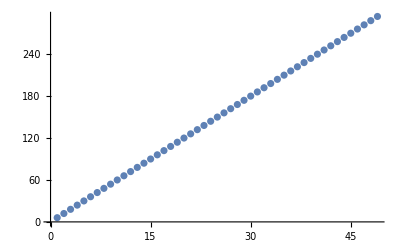

{{1,6},{2,12},{3,18},{4,24},{5,30},{6,36},{7,42},{8,48},{9,54},{10,60},{11,66},{12,72},{13,78},{14,84},{15,90},{16,96},{17,102},{18,108},{19,114},{20,120},{21,126},{22,132},{23,138},{24,144},{25,150},{26,156},{27,162},{28,168},{29,174},{30,180},{31,186},{32,192},{33,198},{34,204},{35,210},{36,216},{37,222},{38,228},{39,234},{40,240},{41,246},{42,252},{43,258},{44,264},{45,270},{46,276},{47,282},{48,288},{49,294}}

run11may21no4

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];

wstream=OpenWrite["run11may21no4"];

degrees={};
For[n=0,n<49,n++;
data={};
For[k=2,k<Length[list],k++;
m=list[[k,1]];
srs=list[[k,2]];
srs=(srs/.x->x*2^6*m^3);
(* Delta diamond-diamond *)
ns=Normal[srs]; (*need srs=list[[k,2]], ns = Normal[srs], etc. *)
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,n];
AppendTo[data,{m,cf*m^(3*n)}]

]; (* k *)
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];

Write[wstream,{n,ip}];

AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Print[degrees];

Close[wstream]
```

```mathematica
stream=OpenRead["run11may21no4"];
list=ReadList[stream];
Close[stream];
numericalterms={};
numerators={};
denominators={};
For[k=0,k<Length[list],k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoMonics[poly];
numericalterm=fim[[1]];
AppendTo[numericalterms,numericalterm]];
table=Table[(-1)^(n+1)*RamanujanTau[n],{n,1,49}];
Print[numericalterms/64-table]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### No reason, but look--

-------------------------------------------------------------------

k 1

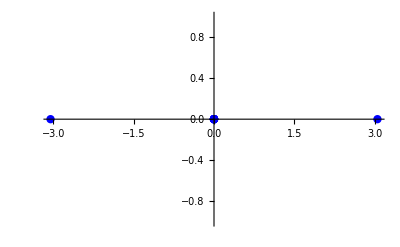

-------------------------------------------------------------------

k 2

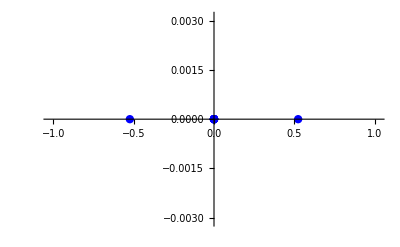

-------------------------------------------------------------------

k 3

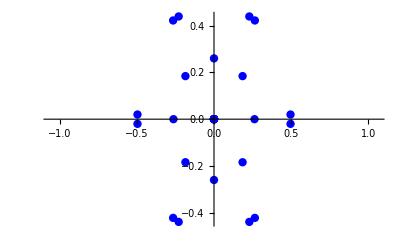

-------------------------------------------------------------------

k 4

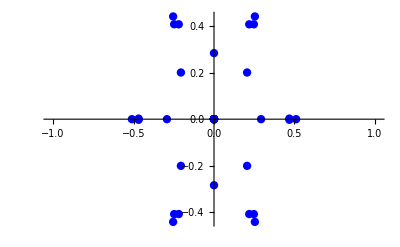

-------------------------------------------------------------------

k 5

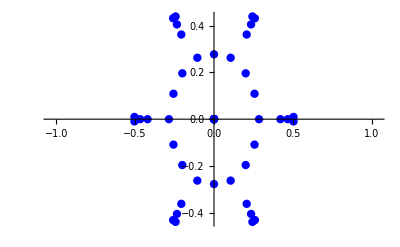

-------------------------------------------------------------------

k 6

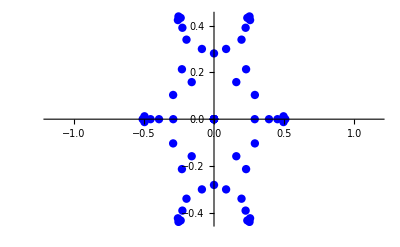

-------------------------------------------------------------------

k 7

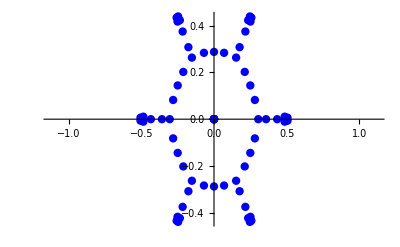

-------------------------------------------------------------------

k 8

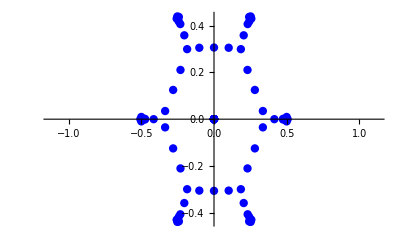

-------------------------------------------------------------------

k 9

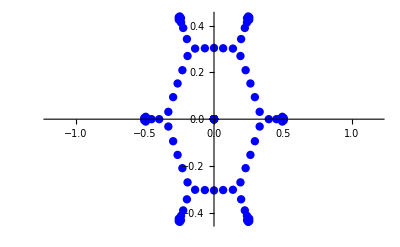

-------------------------------------------------------------------

k 10

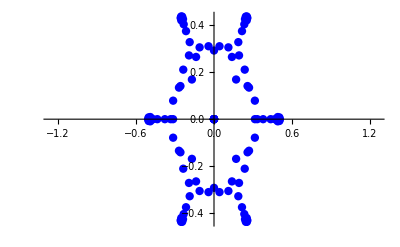

-------------------------------------------------------------------

k 11

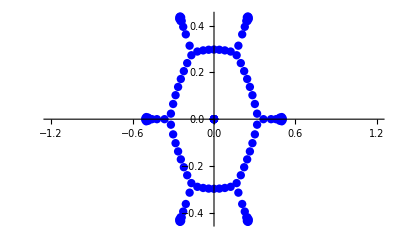

-------------------------------------------------------------------

k 12

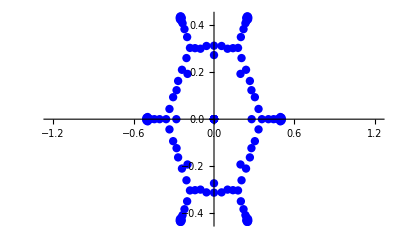

-------------------------------------------------------------------

k 13

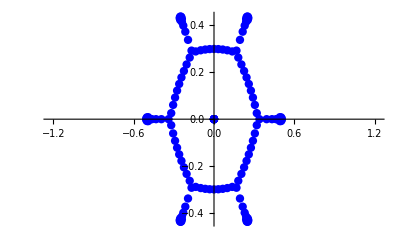

-------------------------------------------------------------------

k 14

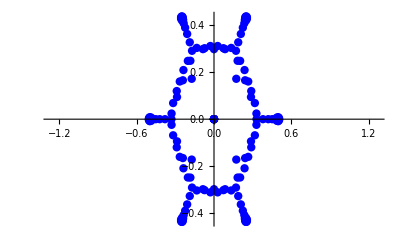

-------------------------------------------------------------------

k 15

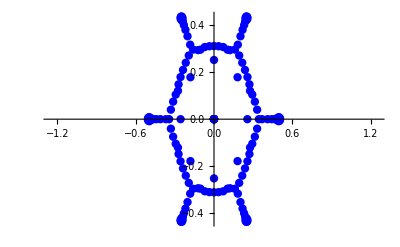

-------------------------------------------------------------------

k 16

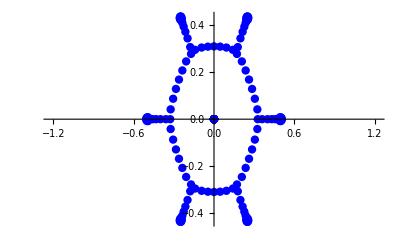

-------------------------------------------------------------------

k 17

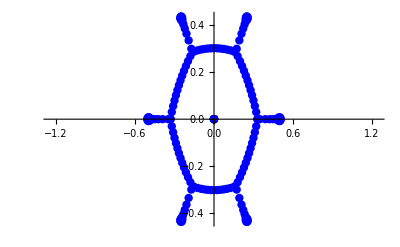

-------------------------------------------------------------------

k 18

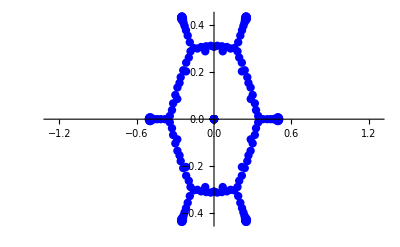

-------------------------------------------------------------------

k 19

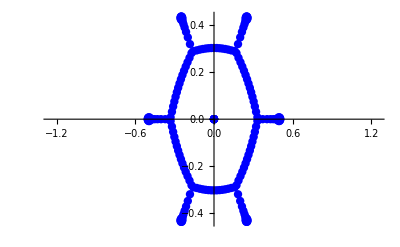

-------------------------------------------------------------------

k 20

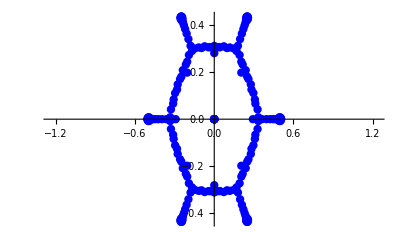

-------------------------------------------------------------------

k 21

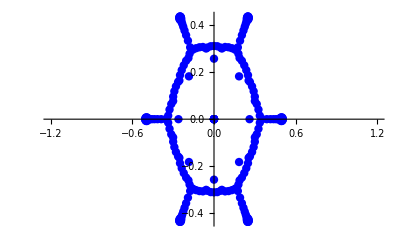

-------------------------------------------------------------------

k 22

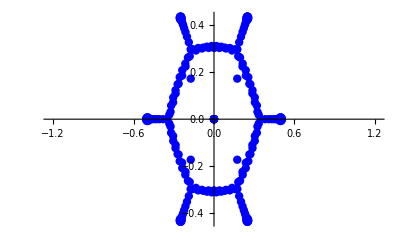

-------------------------------------------------------------------

k 23

$Aborted

```mathematica
color=Blue;
pointsize=.015;
terms=46;
stream=OpenRead["run11may21no4"];
lst=ReadList[stream];
Close[stream];
stream2=OpenWrite["run12may21no1"];
cff[n_]:=lst[[n+2,2]]
sum=Sum[cff[n]*q^n,{n,-1,terms}];
list=Table[Coefficient[sum,q,n],{n,-1,terms}];
productexponents=factorSeriesFromFrrCffList[list,terms-1];
el=Length[productexponents];
pairs={};
un={};
For[k=0,k<el,k++;
Print["-------------------------------------------------------------------"];
Print["k ",k];
poly=productexponents[[k]];
poly=Collect[poly,x];
Write[stream2,{k,poly}];
plotRoots2[poly,x,pointsize,color]]
```

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];
streamw=OpenWrite["run12may21no2"];
For[k=0,k<Length[list],k++;
m=list[[k,1]];
poly=list[[k,2]]/.x->x*2^6*m^3;
poly=Normal[Series[poly,{x,0,25}]];
cl=CoefficientList[poly,x];
terms=Length[cl];
productexponents=factorSeriesFromFrrCffList[cl,terms-1];
Write[streamw,{m,productexponents}]];
Close[streamw]
```

run12may21no2

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];
streamw=OpenWrite["run12may21no2"];
For[k=0,k<Length[list],k++;
m=list[[k,1]];
poly=list[[k,2]]/.x->x*2^6*m^3;
poly=Normal[Series[poly,{x,0,25}]];
cl=CoefficientList[poly,x];
terms=Length[cl];
productexponents=factorSeriesFromFrrCffList[cl,terms-1];
Write[streamw,{m,productexponents}]];
Close[streamw]
```

run12may21no2

```mathematica
stream=OpenRead["run12may21no2"];
list=ReadList[stream];
Close[stream];
firstpe=list[[1,2]];
yes=0;
For[k=0,k<Length[list],k++;
m=list[[k,1]];
pe=list[[k,2]];
If[pe===firstpe,yes++]];
Print[yes]
```

1

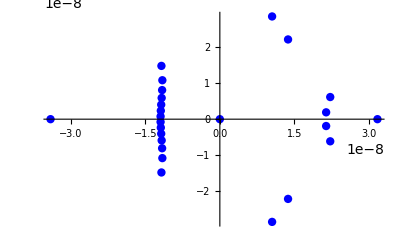

```mathematica
stream=OpenRead["run12may21no2"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
pe=list[[k,2]];
AppendTo[data,{m,pe[[1]]}]
];
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
plotRoots2[poly,x,pointsize,Blue]
```

```mathematica
stream=OpenRead["run24apr21no1"];
list=ReadList[stream];
Close[stream];
streamw=OpenWrite["run12may21no3"];
For[k=0,k<Length[list],k++;
m=list[[k,1]];
poly=list[[k,2]]/.x->x*2^6*m^3;
poly=Normal[Series[poly,{x,0,5}]];
cl=CoefficientList[poly,x];
terms=Length[cl];
productexponents=factorSeriesFromFrrCffList[cl,terms-1];
Write[streamw,{m,productexponents}]];
Close[streamw]
```

run12may21no3

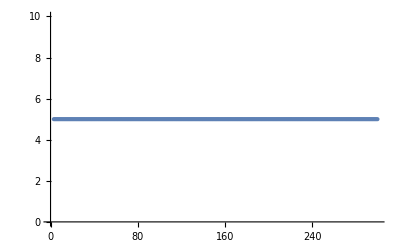

```mathematica
stream=OpenRead["run12may21no3"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
pe=list[[k,2]];
AppendTo[data,{m,Length[pe]}]];
Print[ListPlot[data]]
```

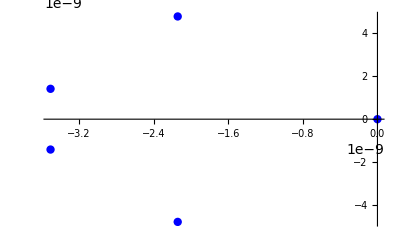

25

```mathematica
stream=OpenRead["run12may21no3"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
pe=list[[k,2]];
AppendTo[data,pe[[1]]]
];
data=data/setGCD[data];
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
plotRoots2[poly,x,pointsize,Blue]
```

```mathematica
stream=OpenRead["run12may21no3"];
list=ReadList[stream];
Close[stream];
data={};
sgdata={};
degreedata={};
For[n=0,n<5,n++;
Print["========================================="];
ndata={};
For[k=0,k<Length[list],k++;
m=list[[k,1]];
pe=list[[k,2]];
AppendTo[data,pe[[n]]];
AppendTo[ndata,pe[[n]]];
];
sg=setGCD[data];
AppendTo[sgdata,sg];
data=data/setGCD[data];
ip=InterpolatingPolynomial[data,x];
ip=Collect[ip,x];
degree=Exponent[ip,x];
AppendTo[degreedata,degree];
plotRoots2[poly,x,pointsize,Blue]];
Print[sgdata];
Print[degreedata]
```

=========================================

-Graphics-

=========================================

-Graphics-

=========================================

-Graphics-

=========================================

-Graphics-

=========================================

-Graphics-

{64,1,1,1/3,1/3}

{3,595,893,1191,1489}